```mathematica
numb1={52};
numb2={52};
latvec1={100,100,100};
latvec2={100,100,100};
sigma={3.401};
epsilon={0.978638};
rad=2.5;
b=8.314462618*^-3*87.3;
cutoff=10;
config1=Table[RandomReal[],#,3]&/@numb1*latvec1[[1]]-latvec1[[1]]/2;

config2=Table[RandomReal[],#,3]&/@numb2*latvec2[[1]]-latvec2[[1]]/2;

configEpbc[config_,cutoff_,latvec_,epsilon_,sigma_]:=Module[{dist,utot},dist=Flatten[Table[If[i==j&&k==l &&a==b==c==0,Nothing,{i,j,EuclideanDistance[config[[i,k]],config[[j,l]]+{a,b,c}*latvec]}],{i,Length[config]},{j,Length[config]},{k,Length[config[[i]]]},{l,Length[config[[j]]]},{a,-1,1},{b,-1,1},{c,-1,1}],6];
utot=Sum[If[i[[3]]>cutoff,0,(((epsilon[[i[[1]]]]+epsilon[[i[[2]]]])^0.5)*(sigma[[i[[1]]]]+sigma[[i[[2]]]])/(2*i[[3]]))^12-(((epsilon[[i[[1]]]]+epsilon[[i[[2]]]])^0.5)*(sigma[[i[[1]]]]+sigma[[i[[2]]]])/(2*i[[3]]))^6],{i,dist}];
N[utot/2]];

randmove[stepleng_]:=Module[{localConfig={config1,config2},cho0,cho,cho1,cho2,oldE,temp,newE,lat={latvec1,latvec2}},
cho0=RandomInteger[{1,2}];
cho=RandomInteger[{1,Length[localConfig[[cho0]]]}];
cho1=RandomInteger[{1,Length[localConfig[[cho0]][[cho]]]}];
cho2=Table[RandomReal[{-1,1}]*stepleng/100,3]*lat[[cho0]];
oldE=configEpbc[localConfig[[cho0]],cutoff,lat[[cho0]],epsilon,sigma];
localConfig[[cho0]][[cho]][[cho1]]=localConfig[[cho0]][[cho]][[cho1]]+cho2;

temp=MapThread[#1>#2&,{lat[[cho0]],localConfig[[cho0]][[cho]][[cho1]]}];
localConfig[[cho0]][[cho]][[cho1]]=MapThread[If[#1,#2,#2-#3]&,{temp,localConfig[[cho0]][[cho]][[cho1]],lat[[cho0]]}];
newE=configEpbc[localConfig[[cho0]],cutoff,lat[[cho0]],epsilon,sigma];
If[RandomReal[]<N[Exp[-b*(newE-oldE)]],localConfig,{config1,config2}]
];

volchange[length_]:=Module[{cho,oldE,lat1=latvec1,lat2=latvec2,con1=config1,con2=config2,newE},
cho=RandomReal[{-1,1}]*length;
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma];
con1=con1*(lat1[[1]]-cho)/lat1[[1]];
con2=con2*(lat2[[1]]+cho)/lat2[[1]];
lat1=lat1+cho;
lat2=lat2-cho;
newE=configEpbc[con1,cutoff,lat1,epsilon,sigma]+configEpbc[con2,cutoff,lat2,epsilon,sigma];
If[RandomReal[]<N[N[Exp[-b*(newE-oldE)]]*((lat1[[1]]^(3*Total[numb1]))*(lat2[[1]]^(3*Total[numb2])))/((latvec1[[1]]^(3*Total[numb1]))*(latvec2[[1]]^(3*Total[numb2])))],{con1,con2,lat1,lat2},{config1,config2,latvec1,latvec2}]
];

den:=(
{numb1[[1]]/latvec1[[1]]^3,numb2[[1]]/latvec2[[1]]^3})
paraexchange[]:=Module[{num,con,cho,cho1,cho2,oldE,lat,newE},
num={numb1,numb2};
con={config1,config2};
lat={latvec1,latvec2};
cho=RandomInteger[{1,2}];
cho1=RandomInteger[{1,Length[con[[cho]]]}];
cho2=RandomInteger[{1,Length[con[[cho]][[cho1]]]}];
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma];
con[[3-cho]][[cho1]]=Append[con[[3-cho]][[cho1]],Table[RandomReal[{-1,1}],3]*lat[[3-cho]]];
con[[cho]][[cho1]]=Delete[con[[cho]][[cho1]],cho2];
newE=configEpbc[con[[1]],cutoff,lat[[1]],epsilon,sigma]+configEpbc[con[[2]],cutoff,lat[[2]],epsilon,sigma];
num[[cho]][[cho1]]=num[[cho]][[cho1]]-1;
num[[3-cho]][[cho1]]=num[[3-cho]][[cho1]]+1;
If[RandomReal[]<N[N[Exp[-b*(newE-oldE)]]*((Total[num[[cho]]]+1)*lat[[3-cho]][[1]]^3)/(Total[num[[3-cho]]]*lat[[cho]][[1]]^3)],{con[[1]],con[[2]],num[[1]],num[[2]]},{config1,config2,numb1,numb2}]
];
configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]
conE={}
densi={}
Table[{config1,config2}=randmove[10];{config1,config2,latvec1,latvec2}=volchange[10];{config1,config2,numb1,numb2}=paraexchange[];conE=Append[conE,configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]];densi=Append[densi,den],50];
Length[config1[[1]]]
Length[config2[[1]]]
numb1
numb2
latvec1
latvec2
configEpbc[config1,cutoff,latvec1,epsilon,sigma]+configEpbc[config2,cutoff,latvec2,epsilon,sigma]
```

-0.25205

{}

{}

General::munfl: Exp[-1775.39] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7242.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-159798.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

39

65

{39}

{65}

{70.5388,70.5388,70.5388}

{129.461,129.461,129.461}

-1.7867

3.67988

```mathematica
ListPointPlot3D[config2[[1]],BoxRatios->{1,1,1},PlotRange->{-latvec2[[1]],latvec2[[1]],-latvec2[[1]],latvec2[[1]],-latvec2[[1]],latvec2[[1]]}]
ListPointPlot3D[config1[[1]],BoxRatios->{1,1,1},PlotRange->{-latvec1[[1]],latvec1[[1]],-latvec1[[1]],latvec1[[1]],-latvec1[[1]],latvec1[[1]]}]
```

Automatic::prng: Value of option PlotRange -> {-129.461,129.461,-129.461,129.461,-129.461,129.461} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

Automatic::prng: Value of option PlotRange -> {-70.5388,70.5388,-70.5388,70.5388,-70.5388,70.5388} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

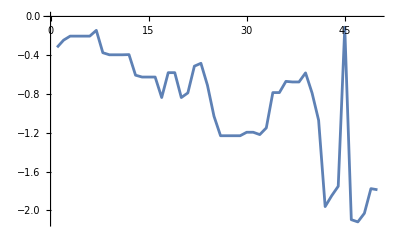

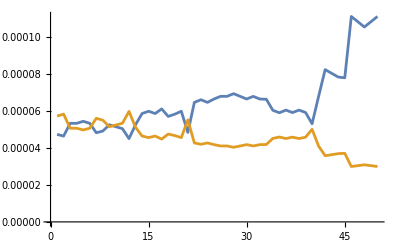

```mathematica
ListLinePlot[conE]
ListLinePlot[Transpose[densi]]
```

```mathematica
Table[{config1,config2}=randmove[10];{config1,config2,latvec1,latvec2}=volchange[10];{config1,config2,numb1,numb2}=paraexchange[],50];
```

{100,100,100}

-Graphics3D-

```mathematica
config1[[1]]
Delete[config1[[1]],1]
```

{{-13.4186,-43.1198,-6.92495},{7.29751,-47.8312,-22.3895},{-32.6203,-10.6598,40.2823},{-44.0713,38.596,0.780806},{8.60782,-4.66496,30.6485},{14.6136,-10.7653,37.3739},{18.9564,49.6214,5.51197},{-34.1367,-29.1992,-29.9533},{48.1458,11.316,-48.0463},{44.9231,2.56253,-47.9621},{-27.4144,44.6808,10.2582},{37.5663,-18.5945,8.59377},{-22.7989,-44.5441,-40.5596},{39.6547,38.7255,27.1176},{-9.8257,47.7553,18.1089},{22.3289,-29.9419,39.5116},{-34.1926,-15.2611,21.5899},{39.1446,-27.4816,24.3334},{15.9466,-25.2262,3.57603},{-17.4293,36.4783,10.3125},{48.7467,24.8678,31.1737},{-31.8242,-12.2751,25.6139},{-35.5537,-1.58773,-46.3442},{-34.9851,-31.3931,-31.2551},{42.3247,-42.5413,6.67233},{39.6638,-36.0492,-33.091},{12.0027,22.0577,-33.59},{13.0558,-3.46775,23.0826},{7.14246,11.8934,37.0481},{48.3142,23.0468,12.6273},{-0.0431172,-36.6451,40.8289},{-35.6468,29.2633,-25.2772},{-4.46803,-43.777,1.44223},{-4.80721,1.92722,33.0764},{22.7807,16.9022,16.3125},{-45.3513,47.0081,-2.60686},{18.5153,5.65413,-34.2423},{-37.4435,23.395,-21.94},{-42.6045,-28.3128,-41.9245},{32.1406,-18.6145,-1.50406},{19.9636,48.4268,-6.13013},{-30.1234,1.81351,-45.4661},{14.0004,-38.1914,-16.5645},{-31.7829,37.8701,-36.2219},{-47.9381,11.882,-34.707},{48.9104,10.3451,-6.21958},{26.5878,-41.094,-19.5947},{1.27164,37.1312,-14.1698},{-25.3211,23.6061,-44.556},{-14.0557,-43.3875,43.1159},{-2.89111,43.0302,0.206496},{9.26587,-18.2102,22.1315},{-3.69103,24.3516,-5.38107},{12.935,15.1408,17.0456},{13.0886,-12.8731,40.378},{1.80445,49.8769,31.4333},{-4.537,41.9906,9.62521},{-5.53465,29.242,-17.1024},{-40.765,-18.2418,-8.98925},{49.3366,33.8585,-0.0714189},{12.1218,-24.1059,-43.2222},{-23.0036,32.6111,33.5098},{31.2416,13.385,44.7635},{-6.66007,41.3517,-26.8685},{3.67671,21.0951,-16.5852},{-42.4832,-30.8868,49.6973},{26.2101,39.5034,-26.2711},{-20.836,44.7167,-35.0032},{43.7967,-2.07656,-1.58574},{31.1276,-42.9514,39.1005},{-13.6326,26.4498,31.2415},{11.3375,2.85684,4.37112},{-42.271,32.8584,-40.5294},{-23.5559,-29.4773,30.2345},{43.6833,15.8869,43.0916},{-30.5881,-35.0148,-31.4927},{-3.35603,-0.530505,21.6609},{42.4534,5.98889,42.6068},{49.5959,-9.65201,9.18885},{-5.77782,45.3117,29.0425}}

{{7.29751,-47.8312,-22.3895},{-32.6203,-10.6598,40.2823},{-44.0713,38.596,0.780806},{8.60782,-4.66496,30.6485},{14.6136,-10.7653,37.3739},{18.9564,49.6214,5.51197},{-34.1367,-29.1992,-29.9533},{48.1458,11.316,-48.0463},{44.9231,2.56253,-47.9621},{-27.4144,44.6808,10.2582},{37.5663,-18.5945,8.59377},{-22.7989,-44.5441,-40.5596},{39.6547,38.7255,27.1176},{-9.8257,47.7553,18.1089},{22.3289,-29.9419,39.5116},{-34.1926,-15.2611,21.5899},{39.1446,-27.4816,24.3334},{15.9466,-25.2262,3.57603},{-17.4293,36.4783,10.3125},{48.7467,24.8678,31.1737},{-31.8242,-12.2751,25.6139},{-35.5537,-1.58773,-46.3442},{-34.9851,-31.3931,-31.2551},{42.3247,-42.5413,6.67233},{39.6638,-36.0492,-33.091},{12.0027,22.0577,-33.59},{13.0558,-3.46775,23.0826},{7.14246,11.8934,37.0481},{48.3142,23.0468,12.6273},{-0.0431172,-36.6451,40.8289},{-35.6468,29.2633,-25.2772},{-4.46803,-43.777,1.44223},{-4.80721,1.92722,33.0764},{22.7807,16.9022,16.3125},{-45.3513,47.0081,-2.60686},{18.5153,5.65413,-34.2423},{-37.4435,23.395,-21.94},{-42.6045,-28.3128,-41.9245},{32.1406,-18.6145,-1.50406},{19.9636,48.4268,-6.13013},{-30.1234,1.81351,-45.4661},{14.0004,-38.1914,-16.5645},{-31.7829,37.8701,-36.2219},{-47.9381,11.882,-34.707},{48.9104,10.3451,-6.21958},{26.5878,-41.094,-19.5947},{1.27164,37.1312,-14.1698},{-25.3211,23.6061,-44.556},{-14.0557,-43.3875,43.1159},{-2.89111,43.0302,0.206496},{9.26587,-18.2102,22.1315},{-3.69103,24.3516,-5.38107},{12.935,15.1408,17.0456},{13.0886,-12.8731,40.378},{1.80445,49.8769,31.4333},{-4.537,41.9906,9.62521},{-5.53465,29.242,-17.1024},{-40.765,-18.2418,-8.98925},{49.3366,33.8585,-0.0714189},{12.1218,-24.1059,-43.2222},{-23.0036,32.6111,33.5098},{31.2416,13.385,44.7635},{-6.66007,41.3517,-26.8685},{3.67671,21.0951,-16.5852},{-42.4832,-30.8868,49.6973},{26.2101,39.5034,-26.2711},{-20.836,44.7167,-35.0032},{43.7967,-2.07656,-1.58574},{31.1276,-42.9514,39.1005},{-13.6326,26.4498,31.2415},{11.3375,2.85684,4.37112},{-42.271,32.8584,-40.5294},{-23.5559,-29.4773,30.2345},{43.6833,15.8869,43.0916},{-30.5881,-35.0148,-31.4927},{-3.35603,-0.530505,21.6609},{42.4534,5.98889,42.6068},{49.5959,-9.65201,9.18885},{-5.77782,45.3117,29.0425}}

```mathematica
Randomreal[{-1,1}]
```

Randomreal[{-1,1}]

```mathematica
config1
```

{{{72.9028,13.4403,-43.4839},{29.5355,-1.61183,8.90786},{-60.3195,8.22255,14.3693},{15.2075,43.7738,-14.6857},{41.2206,-6.05211,-1.63361},{-23.8741,-46.2779,25.7966},{-13.5639,-16.8922,-52.6273},{15.1966,-4.47805,67.1678},{81.6851,70.1918,-53.3558},{-3.68791,14.0482,-61.7943},{21.8159,-41.9076,61.9071},{-0.878077,-7.51451,-17.0749},{30.7219,-58.0871,34.794},{39.1708,48.9614,70.4932},{-30.9468,20.6518,-22.117},{4.76805,-27.2407,49.5485},{18.8408,-30.7293,24.6007},{71.9841,-6.5373,11.8316},{-2.9171,-11.0879,-56.2768},{-42.5364,71.9053,49.9161},{-26.7926,-23.938,79.6143},{-18.6233,-75.7219,-51.5596},{-21.5792,8.12409,-22.5326},{27.0656,33.4265,-44.3001},{-79.5141,60.0532,-109.343},{-44.8487,75.3888,4.54183}}}

```mathematica
configEpbc[config1,cutoff,latvec1,epsilon,sigma]
```

-0.0000123744

```mathematica
config1
cho=RandomInteger[{1,Length[config1]}];
cho1=RandomInteger[{1,Length[config1[[cho]]]}];
cho2=Table[RandomReal[{-1,1}]*10/100,3]*latvec1
oldE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]
tempcon=config1[[cho]][[cho1]]
config1[[cho]][[cho1]]=config1[[cho]][[cho1]]+cho2
temp=MapThread[#1>#2&,{latvec1,config1[[cho]][[cho1]]}]
config1[[cho]][[cho1]]=MapThread[If[#1,#2,#2-#3]&,{temp,config1[[cho]][[cho1]],latvec1}]
newE=configEpbc[config1,cutoff,latvec1,epsilon,sigma]
config1[[cho]][[cho1]]
tempcon
config1[[cho]][[cho1]]=tempcon
```

{{{-36.9985,45.3311,45.343},{-0.643448,-41.8845,37.5908},{40.7089,20.4517,29.8587},{-45.9263,-22.1865,30.3281},{-26.7108,-26.8163,22.4341},{43.6271,32.528,-20.3309},{-21.3561,-35.6359,-14.7915},{18.5569,26.8014,41.2729},{-32.7984,5.4677,-17.9027},{-38.649,-2.81825,29.7841},{-29.6518,-42.6525,-32.3656},{-22.9033,-28.3752,-21.5414},{-44.6113,-11.789,-15.1482},{-49.2843,24.0305,-19.7679},{-25.7658,31.2589,-10.1396},{20.3198,-5.49893,-35.1519},{36.6395,-5.90729,-40.7571},{-35.5939,24.3502,32.9799},{6.06129,38.4053,-45.8847},{-40.7863,31.8692,23.1711},{13.9493,-9.78399,-47.8551},{-31.3617,-1.51047,37.0349},{3.16292,-36.717,-26.4095},{-14.7275,-16.6617,27.7025},{-6.6921,-6.5697,39.2216},{2.33665,-28.4685,-22.9233}}}

{-6.00921,6.58113,4.37747}

-0.0000151241

{-45.9263,-22.1865,30.3281}

{-51.9355,-15.6054,34.7056}

{True,True,True}

{-51.9355,-15.6054,34.7056}

-0.0000151241

{-51.9355,-15.6054,34.7056}

{-45.9263,-22.1865,30.3281}

{-45.9263,-22.1865,30.3281}

```mathematica
Simplify[a]
```

ⅇ^(-0.0000185005 Return)

```mathematica
N[ⅇ^-0.00001850051841889821]
```

0.999981

```mathematica
{2,3}
```

{2,3}

```mathematica
Total[{2,3}]
```

5

Continue::nofwd: No enclosing For, While, Until or Do found for Continue[].

Hold[Continue[]]

{{Atom1 - Atom1,0},{Atom1 - Atom1,2 √3},{Atom1 - Atom1,2 √3},{Atom1 - Atom1,0},{Atom1 - Atom2,0.141421},{Atom1 - Atom2,3.52278},{Atom1 - Atom2,3.34963},{Atom1 - Atom2,0.1},{Atom2 - Atom1,0.141421},{Atom2 - Atom1,3.34963},{Atom2 - Atom1,3.52278},{Atom2 - Atom1,0.1},{Atom2 - Atom2,0.},{Atom2 - Atom2,3.40735},{Atom2 - Atom2,3.40735},{Atom2 - Atom2,0.}}